```mathematica
Global Conditions
```

Conditions Global

```mathematica
cond={e1->.02,e2->.02,b->5,c->1};
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text["ALLD",{-textoffset,-textoffset}]],Graphics[Text["ALLC",{1+textoffset,-textoffset}]],Graphics[Text["DISC",{1/2,Tan[Pi/3]/2+textoffset}]]};
```

```mathematica
SetDirectory["/Users/jplotkin/Research/Arunas - Institutions/NatComm/Revisions/Replications/Replicate Figure 2 Mathematica"];
```

```mathematica
Print["Shunning Strict"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==(g ep+(1-g) e2)^Q,gy==e2^Q,gz==(g ep+(1-g) e2)^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

(*Ternary plot Code from https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots*)
dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSHStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];
Export["imageSHStrict.pdf",imageSHStrict]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSHStrict-vector.pdf",ternplot];
```

Shunning Strict

{0.000415675,0.0004,0.000415675,0.00041254}

{{fx→1.,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→0,fy→-4.25285},{fx→0,fy→-4.25285}}

imageSHStrict.pdf

```mathematica
Print["Shunning Tol"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;

ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-(g ep+(1-g) e2))^Q,gy==1-(1-e2)^Q,gz==1-(1-(g ep+(1-g) e2))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[2]];
piy=b (fx+fz gy) (1-e1)/.soln[[2]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[2]];
pi=fx pix+fy piy+fz piz/.soln[[2]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[1]][[1,2]],equillibria[[1]][[2,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSHTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSHTol.pdf",imageSHTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None,VectorPoints->24,VectorScaling->Automatic,StreamPoints->Fine];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSHTol-vector.pdf",ternplot]
```

Shunning Tol

{0.922643,0.0396,0.922643,0.746035}

{{fx→0,fy→0.888898},{fx→0,fy→0.888898},{fx→0,fy→0.888898},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→0.793022,fy→-0.00160256}}

imageSHTol.pdf

imageSHTol-vector.pdf

```mathematica
Print["Shunning E=0 no institution"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==(g ep+(1-g) e2),
gy==e2,
gz==(g2 ep+2 d2 e2 + b2 e2),
g==fx gx+fy gy+fz gz,
g2==fx gx^2+fy gy^2+fz gz^2,
b2 == 1 -2 g + g2,
d2 == g-g2
},
{gx,gy,gz,g2,b2,d2,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}]
};


dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSHE0=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSHE0.pdf",imageSHE0]
```

Shunning E=0 no institution

{0.0468041,0.02,0.020899,0.0284907}

imageSHE0.pdf

```mathematica
Print["Scoring Strict"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==ep^Q,gy==e2^Q,gz==(g ep+(1-g) e2)^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[1]][[2,2]],equillibria[[1]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCStrict.pdf",imageSCStrict];

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSCStrict-vector.pdf",ternplot];
```

Scoring Strict

{0.923137,0.0004,0.110679,0.332361}

{{fy→0,fx→0.88391},{fy→0,fx→0.88391},{fy→0.783687,fx→-0.000433493},{fy→0.783687,fx→-0.000433493},{fy→-0.0832993,fx→0.866553},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0}}

```mathematica
Print["Scoring Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-ep)^Q,gy==1-(1-e2)^Q,gz==1-(1-(g ep+(1-g) e2))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[2]];
piy=b (fx+fz gy) (1-e1)/.soln[[2]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[2]];
pi=fx pix+fy piy+fz piz/.soln[[2]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria-- this computes fine but gives diff restults than origi submission*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]
(*equil at DISC only b/c blowup at ALLD,but ALLD is an equil:*)
(*
{vx,vy}/.{fx->0,fy->1}
{vx,vy}/.{fx->0,fy->.9999}
{vx,vy}/.{fx->0,fy->.9}
*)

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[1]][[2,2]],equillibria[[1]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCTol.pdf",imageSCTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None,VectorPoints->30];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSCTol-vector.pdf",ternplot]
```

Scoring Tolerant

{0.998463,0.0396,0.937668,0.776293}

{{fy→0.888898,fx→0},{fy→0.832719,fx→-0.0412989},{fy→0.832719,fx→-0.0412989},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-1.65045},{fy→0,fx→-1.65045}}

imageSCTol.pdf

imageSCTol-vector.pdf

```mathematica
Print["Scoring E=0 no institution"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==ep,
gy==e2,
gz==g ep+(1-g)e2,
g==fx gx+fy gy+fz gz
},
{gx,gy,gz,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

otherequil=FindRoot[Evaluate[vy] /. fx->0,{fy,.75}][[1,2]]
{vx,vy} /. {fx->0,fy->.787415}

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

otherdots=Table[
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[ep,FindRoot[Evaluate[vy] /. fx->ep,{fy,.75}][[1,2]]],diskradius]}]
,{ep,0,.787,.03}];

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCE0=Show[ternplot,dots,otherdots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCE0.pdf",imageSCE0]
```

Scoring E=0 no institution

{0.9608,0.02,0.55691,0.570695}

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 fx)/87992-(121001 fy)/175984 == 1.

{{fx→-4.2664,fy→5.05382}}

0.787415

{0.,6.56179×10^-10}

imageSCE0.pdf

```mathematica
Print["SS Strict"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==(g ep+(1-g)(1-e2))^Q,gy==(g e2+(1-g)(1-e2))^Q,gz==(g ep+(1-g)(1-e2))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[5]][[1,2]],equillibria[[5]][[2,2]]],diskradius]}]
};


dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSStrict.pdf",imageSSStrict];

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];

Export["imageSSStrict-vector.pdf",ternplot]
```

SS Strict

{0.932074,0.0634924,0.932074,0.758357}

{{fx→1.,fy→-2.72635×10^-10},{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→0,fy→0.862886},{fx→0,fy→1.},{fx→0,fy→1.}}

imageSSStrict-vector.pdf

```mathematica
Print["SS Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-(g ep+(1-g)(1-e2)))^Q,gy==1-(1-(g e2+(1-g)(1-e2)))^Q,gz==1-(1-(g ep+(1-g)(1-e2)))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

soln2simple=FullSimplify[soln[[2]],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln2simple;
piy=b (fx+fz gy) (1-e1)/.soln2simple;
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln2simple;
pi=fx pix+fy piy+fz piz/.soln2simple;

fxdot[fx_,fy_,fz_]=Simplify[fx (pix-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
fydot[fx_,fy_,fz_]=Simplify[fy (piy-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
fzdot[fx_,fy_,fz_]=Simplify[fz (piz-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];

(*
vxanalytic=Simplify[fxdot[fx,fy,1-fy-fx],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
vyanalytic=Simplify[fydot[fx,fy,1-fy-fx],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
 Solve[{vxanalytic==0,vyanalytic==0},{fx,fy}]
*)

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[11]][[1,2]],equillibria[[11]][[2,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSTol.pdf",imageSSTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSSTolt-vector.pdf",ternplot]
```

SS Tolerant

{0.998671,0.289943,0.998671,0.856926}

{{fx→0.0000521364-0.000658821 ⅈ,fy→-0.000344444-0.0000639353 ⅈ},{fx→0.0000521307-0.000658823 ⅈ,fy→-0.000344445-0.0000639329 ⅈ},{fx→-0.000218715-0.000811746 ⅈ,fy→-0.000449456+0.0000838497 ⅈ},{fx→-0.000218725-0.000811745 ⅈ,fy→-0.000449456+0.000083853 ⅈ},{fx→1.,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→0.699492}}

imageSSTol.pdf

imageSSTolt-vector.pdf

```mathematica
Print["SS E=0 no institution"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==g ep+(1-g)(1- e2),
gy==g e2 + (1-g)(1-e2),
gz==(g2 ep+ d2 + b2(1- e2)),
g==fx gx+fy gy+fz gz,
g2==fx gx^2+fy gy^2+fz gz^2,
b2 == 1 -2 g + g2,
d2 == (g-g2)
},
{gx,gy,gz,g2,b2,d2,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[equillibria[[4]][[2,2]],equillibria[[4]][[1,2]]],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[11]][[2,2]],equillibria[[11]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSE0=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSE0.pdf",imageSSE0]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSSE0-vector.pdf",ternplot]
```

SS E=0 no institution

{0.965194,0.239709,0.867272,0.771136}

{{fy→1.+3.3766×10^-7 ⅈ,fx→-8.63974×10^-8+3.08911×10^-8 ⅈ},{fy→0,fx→0.775173+1.98675×10^-10 ⅈ},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→1.0124×10^-10,fx→0.775173+3.9755×10^-10 ⅈ},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→0},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}}

imageSSE0.pdf

imageSSE0-vector.pdf

```mathematica
{gx,gy,gz,g,g2+b2+d2}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}
```

{0.965194,0.239709,0.867272,0.771136,0.895916}

```mathematica
Print["SJ Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-(g ep+(1-g)(1-ep)))^Q,gy==1-(1-(g e2+(1-g)(1-e2)))^Q,gz==1-(1-(g ep+(1-g)(1-e2)))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[2]];
piy=b (fx+fz gy) (1-e1)/.soln[[2]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[2]];
pi=fx pix+fy piy+fz piz/.soln[[2]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[4]][[2,2]],equillibria[[4]][[1,2]]],diskradius]}]
};


dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSJTol.pdf",imageSJTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSJTol-vector.pdf",ternplot]
```

SJ Tolerant

{0.968546,0.300952,0.998681,0.850095}

{{fy→0,fx→0},{fy→-3.85277×10^-7+1.68622×10^-6 ⅈ,fx→0.0000646493+0.0000124643 ⅈ},{fy→0.0000111905+0.0000661882 ⅈ,fx→0.00278724-0.000667156 ⅈ},{fy→0.699492,fx→0},{fy→0,fx→1.},{fy→0,fx→1.},{fy→1.,fx→0},{fy→1.,fx→0},{fy→0,fx→1.25019},{fy→0,fx→1.25019},{fy→0,fx→1.25019},{fy→0,fx→1.25019}}

imageSJTol.pdf

imageSJTol-vector.pdf

```mathematica
Print["SJ Strict"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==(g ep+(1-g)(1-ep))^Q,
gy==(g e2+(1-g)(1-e2))^Q,
gz==(g ep+(1-g)(1-e2))^Q,
g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

otherequil=FindRoot[vy /. fx->0,{fy,.876}][[1,2]];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,otherequil],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSJStrict.pdf",imageSJStrict]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSJStrict-vector.pdf",ternplot]
```

SJ Strict

{0.359537,0.157003,0.937653,0.608088}

{{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→1.0016,fy→0.206978},{fx→1.0016,fy→0.206978},{fx→1.0016,fy→0.206978},{fx→1.25833,fy→0}}

imageSJStrict.pdf

imageSJStrict-vector.pdf

```mathematica
Print["SJ E=0 no institution"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==g ep+(1-g) (1-ep),
gy==g e2+(1-g)(1-e2),
gz==(g2 ep+ d2(e2+1-ep) + b2(1- e2)),
g==fx gx+fy gy+fz gz,
g2==fx gx^2+fy gy^2+fz gz^2,
b2 == 1 -2 g + g2,
d2 == (g-g2)
},
{gx,gy,gz,g2,b2,d2,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJE0=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];
Export["imageSJE0.pdf",imageSJE0];
```

SJ E=0 no institution

{0.5,0.5,0.5,0.5}

{{fx→1.,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→-1.43215},{fx→0,fy→1.},{fx→0,fy→1.}}

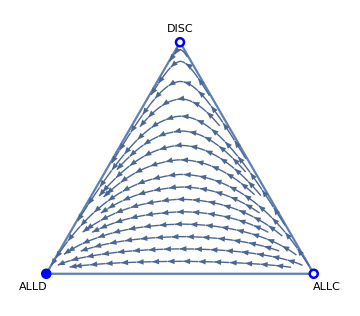

```mathematica
imageSJE0=Show[vlabels,ternplot,dots, ImageSize->Medium,Frame->False,PlotRangePadding->.1]
```

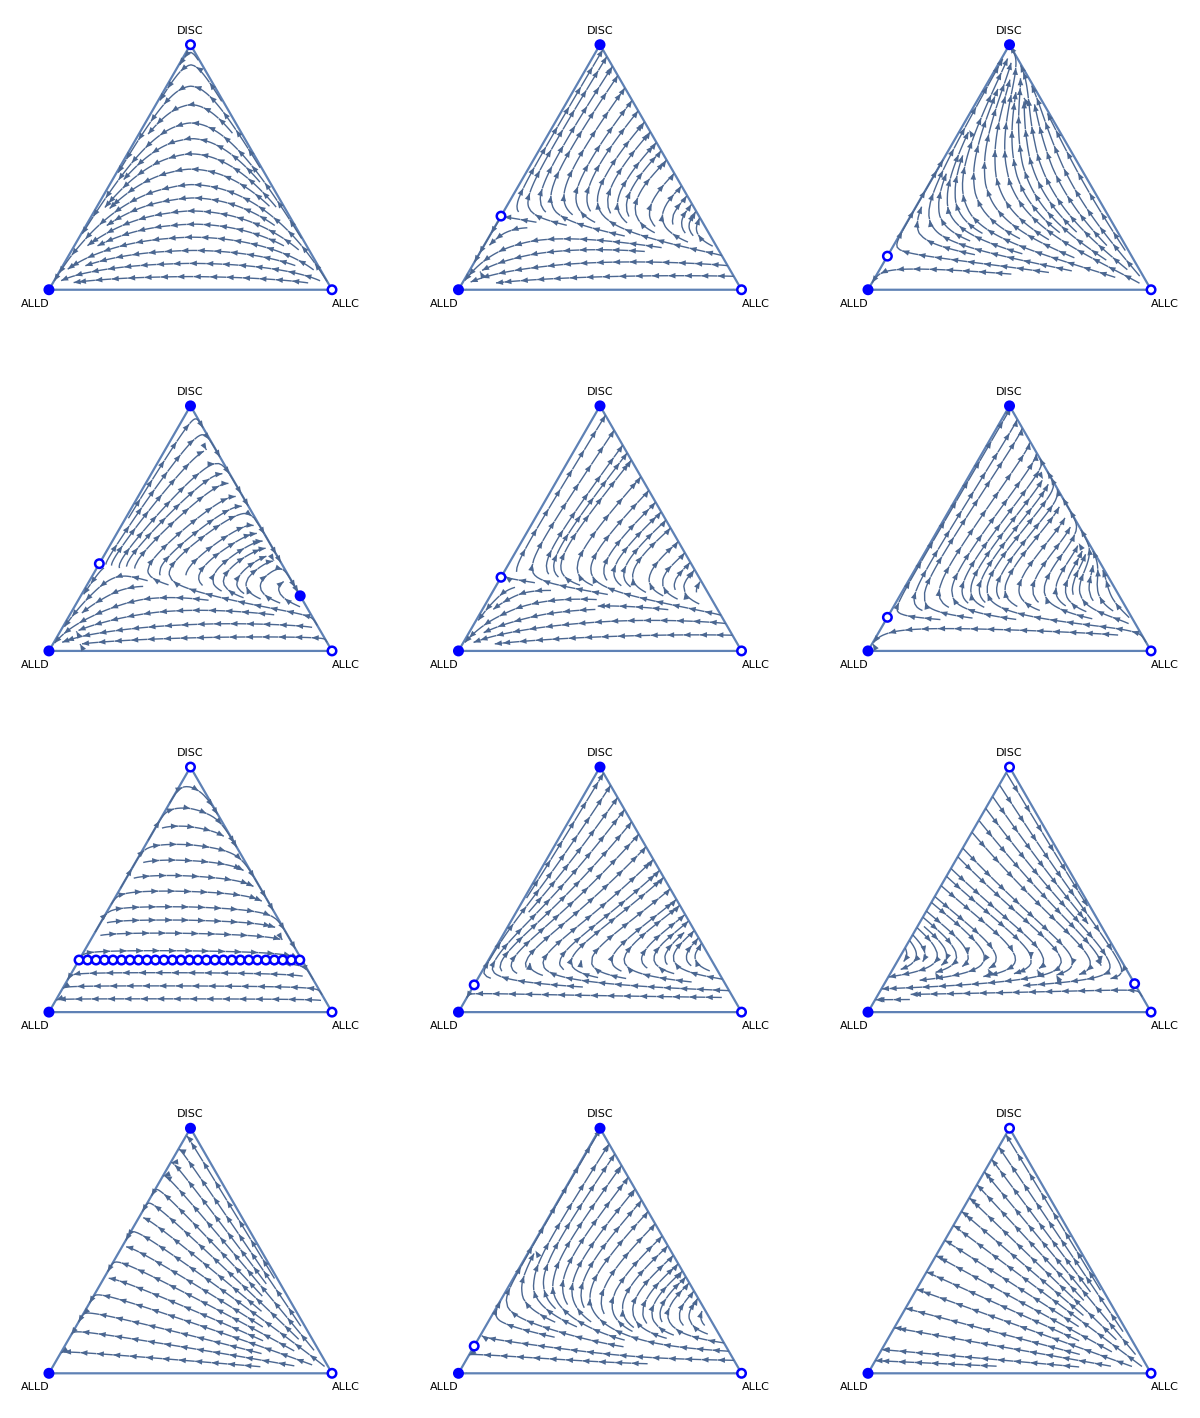

```mathematica
allimages=GraphicsGrid[{{imageSJE0,imageSJTol,imageSJStrict},{imageSSE0,imageSSTol,imageSSStrict},{imageSCE0,imageSCTol,imageSCStrict},{imageSHE0,imageSHTol,imageSHStrict}}]
```

```mathematica
Export["allimages.pdf",allimages];
```